# Backtest on Simulated Data

## This is part 2 of 2 of the supplemental material for Sec. 11.

Instructions: Read performance data from storage after running the C program.

Usage note: 
 - The notebook that generates historical prices simulates and writes all runs at once (sequentially but automatically). 
 - The C program that determines the optimal policy for all states and stages, then imports the historical prices and executes the optimal policy on them, also processes all runs (again, sequentially but automatically). 
 - In contrast, this notebook works per run. Choose which run to import here:

```mathematica
run=1;
```

## Import Performance Results

### Read Directory

```mathematica
readDirectory=ParentDirectory[NotebookDirectory[]]<>"/files/examples";
```

```mathematica
SetDirectory@readDirectory
```

### Display the Game Parameters used in the Dynamic-Programming Code

```mathematica
gameParameters=Import["gameParameters.txt"]
```

***************
Game parameters
***************

Number of games: 1
Temporal increment: 0.0100
Total time: 1.0000
Number of rounds per game: 100
Log-price increment: 0.1000
Maximum log-price: 10.0000
Size of log-price grid: 201
Log-wealth increment: 0.1000
Maximum log-wealth: 10.0000
Size of log-wealth grid: 201
Volatility: 1.0000
Asymptotic mean: 0.3100
Mean-reversion speed: 0.2600
Interest rate: 0.0200

#### Set Those Parameters for This Notebook

```mathematica
σ=1;m=0.31;θ=0.26;r=0.02;
```

### Read a price history from storage

```mathematica
priceHistoryDirectory=readDirectory<>"/"<>ToString@run;
```

```mathematica
SetDirectory@priceHistoryDirectory
```

```mathematica
priceHistory=Flatten@Import["priceHistory.csv"]
```

{1.,1.126,1.104,1.074,1.213,1.075,1.037,1.152,1.106,1.136,1.293,1.201,0.9261,0.806,0.7827,0.7611,0.7025,0.7228,0.769,0.7255,0.6597,0.738,0.8181,0.9349,1.165,1.148,1.182,1.125,1.261,1.32,1.453,1.928,2.3,2.547,2.62,2.71,2.787,2.864,3.016,3.247,2.936,2.629,2.683,2.675,3.078,2.91,3.026,2.899,3.001,3.199,3.272,3.178,3.196,3.321,3.439,3.188,3.252,3.472,4.174,4.074,3.936,4.383,4.394,3.919,4.156,4.158,3.918,4.047,3.906,3.433,2.855,3.208,3.707,3.318,3.718,3.416,3.659,4.001,4.564,3.791,3.958,3.734,3.335,3.535,3.37,3.51,3.468,3.175,3.182,3.252,2.986,3.119,3.005,2.55,2.097,1.929,2.059,1.952,1.828,1.893,2.11}

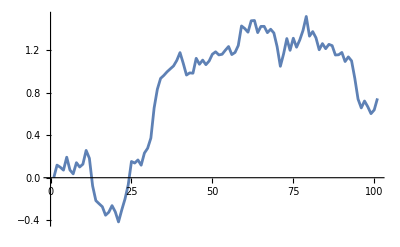

```mathematica
ListLinePlot[Log@priceHistory]
```

```mathematica
performanceDirectory=readDirectory<>"/"<>ToString@run<>"/performance";
```

```mathematica
SetDirectory@performanceDirectory
```

```mathematica
FileNames[]
```

```mathematica
utilityFunctions={"log","target"};
```

```mathematica
performance=Import[performanceDirectory<>"/performance_"<>#<>".csv"]&/@utilityFunctions;
```

```mathematica
T=1;dt=0.01;
```

```mathematica
times=Table[t,{t,0,T,dt}]; (* to-do: streamline this and everything below *)
```

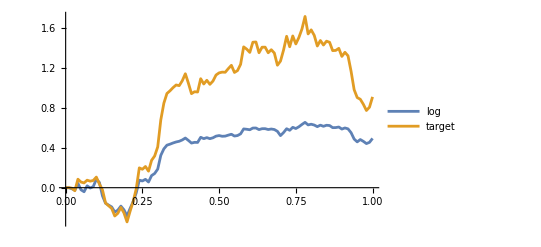

```mathematica
ListLinePlot[{
Thread@{times,Flatten@performance[[1]]},
Thread@{times,Flatten@performance[[2]]}
},
PlotRange->All,PlotLegends->{
utilityFunctions[[1]],
utilityFunctions[[2]]
}]
```

### Policy

#### Analytic result

The analytic result for an interior maximum under log-utility is the optimal policy [see Eqs. (11.10) and (10.18) in the paper]

w=(a(S)-r)/σ^2=1/σ^2[μ(x)+σ^2/2-r]
     =1/σ^2[-θ(x-m)+σ^2/2-r]
     =1/σ^2{-θ [ln(S/S_0)-m]+σ^2/2-r}
     =1/σ^2{-θ ln(S/S_0)+θ m +σ^2/2-r}
     =1/σ^2(θ m +σ^2/2-r)[1-θ/(θ m + σ^2/2 - r)ln(S/S_0)] .

```mathematica
S0=1;
```

```mathematica
F[S_]:=1-θ/(θ m+1/2 σ^2-r)Log[S/S0]
```

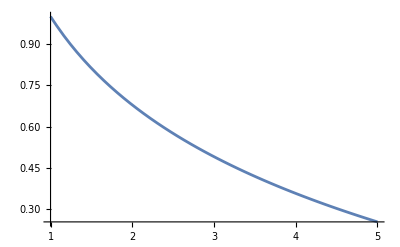

```mathematica
Plot[F[S],{S,1,5}]
```

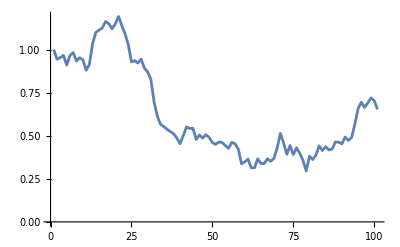

```mathematica
ListLinePlot[F/@priceHistory]
```

```mathematica
μ[S_]:=1/σ^2(θ m+1/2 σ^2-r)F[S]
```

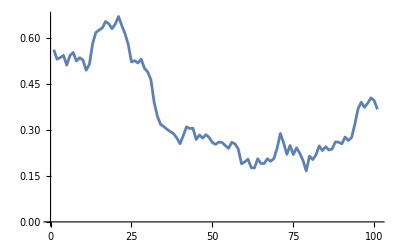

```mathematica
ListLinePlot[μ/@priceHistory]
```

```mathematica
analyticPolicy=F/@priceHistory;(* Without the overall scale of (θ m +σ^2/2 - r)/σ^2*)
```

#### Numerical results

```mathematica
policy=Import[performanceDirectory<>"/policy_"<>#<>".csv"]&/@utilityFunctions;
```

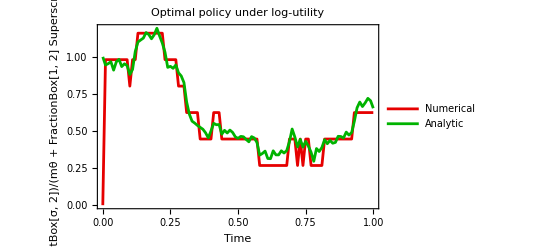

```mathematica
ListLinePlot[{Thread@{times,Flatten@(policy[[1]]/((m θ+1/2 σ^2-r)/σ^2))},Thread@{times,analyticPolicy}},
PlotRange->{All,All},
PlotLegends->{"Numerical","Analytic"},
PlotLabel->Style["Optimal policy under log-utility",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",FontSize->12],Style["(w SuperscriptBox[σ, 2])/(mθ + FractionBox[1, 2] SuperscriptBox[σ, 2] - r)",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->{
RGBColor[0.9,0,0],
RGBColor[0,0.7,0]
}
]
```

```mathematica
rawAnalyticPolicy=μ/@priceHistory;
```

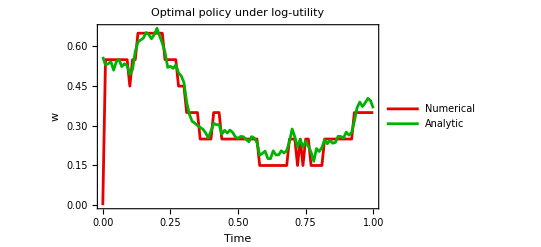

```mathematica
comparisonPlot=ListLinePlot[{Thread@{times,Flatten@policy[[1]]},Thread@{times,rawAnalyticPolicy}},
PlotRange->{All,All},
PlotLegends->{"Numerical","Analytic"},
PlotLabel->Style["Optimal policy under log-utility",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",FontSize->12],Style["w",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->{
RGBColor[0.9,0,0],
RGBColor[0,0.7,0]
}
]
```

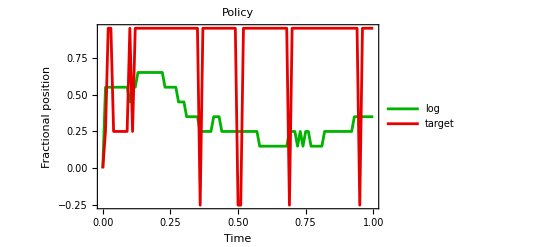

```mathematica
policyPlot=ListLinePlot[{Thread@{times,Flatten@policy[[1]]},Thread@{times,Flatten@policy[[2]]}},
PlotLegends->utilityFunctions,
PlotRange->All,
PlotLabel->Style["Policy",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",FontSize->12],Style["Fractional position",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->{
RGBColor[0,0.7,0],
RGBColor[0.9,0,0]
}]
```

### Trades

```mathematica
trades=Import[performanceDirectory<>"/trades_"<>#<>".csv"]&/@utilityFunctions;
```

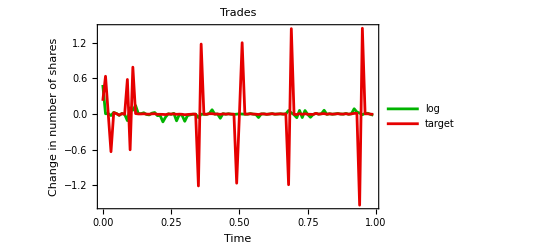

```mathematica
tradePlot=ListLinePlot[{
Thread@{Drop[times,-1],Flatten@trades[[1]]},
Thread@{Drop[times,-1],Flatten@trades[[2]]}
},
PlotLegends->utilityFunctions,
PlotRange->All,
PlotLabel->Style["Trades",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",FontSize->12],Style["Change in number of shares",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->{
RGBColor[0,0.7,0],
RGBColor[0.9,0,0]
}]
```

### Compare performance against arbitrary policies

```mathematica
FileNames[]
```

```mathematica
performanceAllCash=Import[performanceDirectory<>"/performance_allCash.csv"];
```

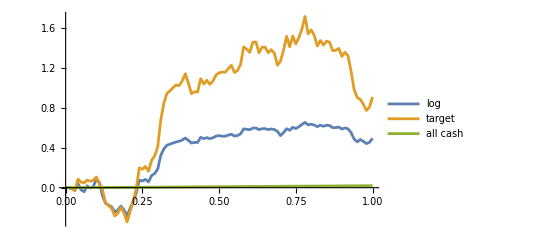

```mathematica
ListLinePlot[{
Thread@{times,Flatten@performance[[1]]},
Thread@{times,Flatten@performance[[2]]},
Thread@{times,Flatten@performanceAllCash}
},
PlotRange->All,PlotLegends->{
utilityFunctions[[1]],
utilityFunctions[[2]],
"all cash"
}]
```

```mathematica
performanceAllStock=Import[performanceDirectory<>"/performance_allStock.csv"];
```

```mathematica
performanceHalf=Import[performanceDirectory<>"/performance_half.csv"];
```

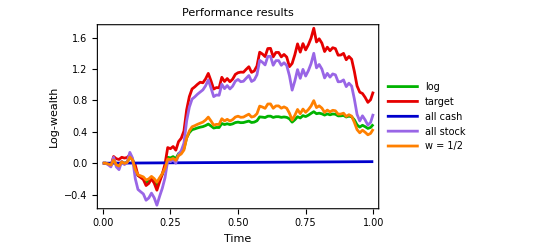

```mathematica
performancePlot=ListLinePlot[{
Thread@{times,Flatten@performance[[1]]},
Thread@{times,Flatten@performance[[2]]},
Thread@{times,Flatten@performanceAllCash},
Thread@{times,Flatten@performanceAllStock},
Thread@{times,Flatten@performanceHalf}
},
PlotRange->All,
PlotLabel->Style["Performance results",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",FontSize->12],Style["Log-wealth",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotLegends->{
utilityFunctions[[1]],
utilityFunctions[[2]],
"all cash", 
"all stock", 
"w = 1/2"
},
PlotStyle->{
RGBColor[0,0.7,0],
RGBColor[0.9,0,0],
RGBColor[0,0,0.8],
RGBColor[0.6,0.4,0.9],
Orange
}
]
```

```mathematica
gameParameters
```

***************
Game parameters
***************

Number of games: 1
Temporal increment: 0.0100
Total time: 1.0000
Number of rounds per game: 100
Log-price increment: 0.1000
Maximum log-price: 10.0000
Size of log-price grid: 201
Log-wealth increment: 0.1000
Maximum log-wealth: 10.0000
Size of log-wealth grid: 201
Volatility: 1.0000
Asymptotic mean: 0.3100
Mean-reversion speed: 0.2600
Interest rate: 0.0200

## Export the plots

### Write Directory

```mathematica
writeDirectory=ParentDirectory[NotebookDirectory[]]<>"/files/examples"<>"/"<>ToString@run<>"/performance";
```

```mathematica
SetDirectory@writeDirectory
```

```mathematica
Export["comparisonPlot_example"<>ToString@run<>".pdf",comparisonPlot]
```

comparisonPlot_example5.pdf

```mathematica
Export["policyPlot_example"<>ToString@run<>".pdf",policyPlot]
```

policyPlot_example5.pdf

```mathematica
Export["tradePlot_example"<>ToString@run<>".pdf",tradePlot]
```

tradePlot_example5.pdf

```mathematica
Export["performancePlot_example"<>ToString@run<>".pdf",performancePlot]
```

performancePlot_example5.pdf